Working Directory: C:\Users\Prajwal\Dropbox\nEDM\psi-nedm\Analysis

(ASCII) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

Runs in the list: 11159

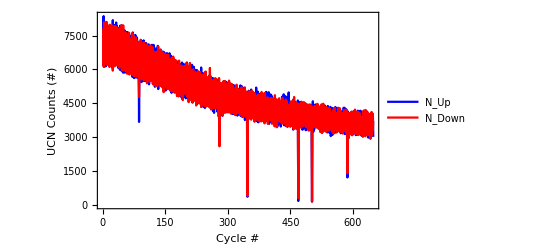

Number of Cycles: 679.

```mathematica
OS="win";(*or linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\psi-nedm\\Analysis"]];
Print["(ASCII) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];
];
If[OS=="linux",
Print["Working Directory:",curDir=SetDirectory["/home/prajwal/Dropbox/nEDM/psi-nedm/Analysis"]];
Print["(faster) Rawdata Directory:",fastDir="/home/prajwal/nEDM/rawdata"];
Print["(ASCII) Rawdata Directory:",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];
];
Print["Runs in the list: ",runNum=11159];
metaStructure={Real,Word,Real,Real,Real,Real,Real};
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
metadata=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum,10,6],"\\",IntegerString[runNum,10,6],"_Meta3.edm"],metaStructure2];
EDAListPlot[metadata[[2;;650,27]],metadata[[2;;650,28]],PlotLegends->{"N_Up","N_Down"},PlotStyle->{Blue,Red,Gray},Joined->True,PlotRange->Full,Frame->True,PlotRange->Full,FrameLabel->{"Cycle #","UCN Counts (#)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},ImageSize->{1000}]
Print["Number of Cycles: ",maxCy=metadata[[-1]][[2]]];
```

```mathematica
brstdat=Table[{0,0,0,0},{k,1,maxCy}];
```

```mathematica
Monitor[
data={};
For[runi=636,runi≤maxCy,runi++,
If[runi== 20||runi==22||runi==90||runi==72||runi==145||runi==283||runi==289||runi==301||runi==323||runi==326||runi==477||runi==526||runi==556||runi==580||runi==600||runi==637,
brstdat[[runi]]={metadata[[runi]][[1]],runi,10,10};
Continue[];
];
data=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum,10,6],"\\",IntegerString[runNum,10,6],"_UCNdet_",IntegerString[runi,10,3],"_0001.fast.ascii"],metaStructure];
dimdata=Dimensions[data][[1]];
brstcoua=0;
brstcoub=0;
For[i=2,i≤dimdata,i++,
If[((data[[i]][[4]]-data[[i-1]][[4]]<1000)&&(data[[i]][[4]]≥218000000000)),
If[data[[i]][[3]]<10,brstcoua++];
If[data[[i]][[3]]>10,brstcoub++];
];
];
brstdat[[runi]]={metadata[[runi]][[1]],runi,brstcoua,brstcoub};
];,
ProgressIndicator[runi/maxCy,ImageSize->{1000,100}]];
Export[StringJoin[ToString[runNum],"_BurstEvents.dat"],brstdat];
ProgressIndicator[1,ImageSize->{1000,100}]
```

## Independent of above section

```mathematica
Print["Runs in the list: ",runNum=11159];
metaStructure3={Word,Real,Real,Real};
brstdata=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum,10,6],"\\",IntegerString[runNum,10,5],"_BurstEvents.dat"],metaStructure3];
Print["# Cycles = ",maxCy=metadata[[-1]][[2]]];
aCy=Round[(maxCy-4)/4];
mult=.000003902;
fita[ftdata_]:=(
nlm=NonlinearModelFit[ftdata,(-bb Cos[((xx-cc)*2Pi)/(180*mult)]),{{bb,.8},{cc,Mean[ftdata[[;;,1]]]}},xx];Return[{{bb/.nlm[[1]][[2]],nlm["ParameterErrors"][[1]]},{cc/.nlm[[1]][[2]],nlm["ParameterErrors"][[2]]}}];
);
fitln[ftdata_]:=(
nlm=NonlinearModelFit[ftdata,(bb xx + cc),{{bb,0},{cc,Mean[fitsareal[[;;,1]][[;;,1]]]}},xx];Return[{{bb/.nlm[[1]][[2]],nlm["ParameterErrors"][[1]]},{cc/.nlm[[1]][[2]],nlm["ParameterErrors"][[2]]}}];
);
fitsa=Table[{{0,0},{0,0}},{k,1,aCy}];
pts=Table[{0,0},{k,1,4}];
aerr=Table[0,{k,1,maxCy-3}];
ptpts={};
For[i=1,i≤maxCy-4,i+=4,
For[j=0,j≤3,j++,
pts[[j+1]]={N[metadata[[i+j]][[-1]]/metadata[[i+j]][[-5]]],N[((brstdata[[i+j]][[3]]-brstdata[[i+j]][[4]])/(brstdata[[i+j]][[3]]+brstdata[[i+j]][[4]]))]};
aerr[[i+j]]=(Sqrt[brstdata[[i+j]][[3]]]+Sqrt[brstdata[[i+j]][[4]]])*Sqrt[2]/(brstdata[[i+j]][[3]]+brstdata[[i+j]][[4]]);
];
fitsa[[Round[((i-1)/4)+1]]]=fita[pts];
AppendTo[ptpts,pts];
];
dispplot=Table[{Flatten[ptpts,1][[k]][[1]],{Flatten[ptpts,1][[k]][[2]],aerr[[k]]}},{k,1,aCy}];
dispplot=Table[{Flatten[ptpts,1][[k]][[1]],{Flatten[ptpts,1][[k]][[2]],aerr[[k]]}},{k,1,aCy}];
fitsareal=Select[fitsa,(#[[1]][[1]]<10&&#[[1]][[1]]>-10)&];
Print["#Ramsey Clusters  = ",Dimensions[fitsa][[1]]];
Print["Filtered #Ramsey Clusters  = ",dimfitsar=Dimensions[fitsareal][[1]]];
errptspt=Table[{k,{fitsareal[[;;,1]][[;;,1]][[k]],fitsareal[[;;,1]][[;;,2]][[k]]}},{k,1,dimfitsar}];
errptsptres=Table[N[fitsareal[[;;,1]][[;;,1]][[k]]-RootMeanSquare[fitsareal[[;;,1]][[;;,1]]]],{k,1,dimfitsar}];
Print["Alpha = ",Mean[fitsareal[[;;,1]][[;;,1]]]];
Print["Alpha Error = ",rmserra=RootMeanSquare[fitsareal[[;;,1]][[;;,2]]]];
Print["A error = ",RootMeanSquare[aerr]];
Print["bb x + cc : ",fitaln=fitln[Table[{k,fitsareal[[;;,1]][[;;,1]][[k]]},{k,1,dimfitsar}]]];
```

Runs in the list: 11159

# Cycles = 679.

#Ramsey Clusters  = 169

Filtered #Ramsey Clusters  = 169

Alpha = 0.0189871

Alpha Error = 0.965533

A error = 0.404885

bb x + cc : {{-0.000831972,0.00113088},{0.0897047,0.110832}}

0.0189871

0.716235

3.84244

0.0000968647

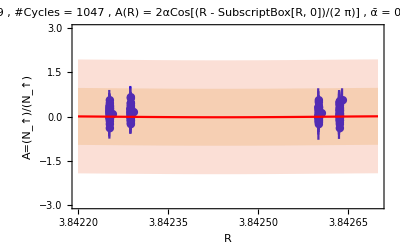

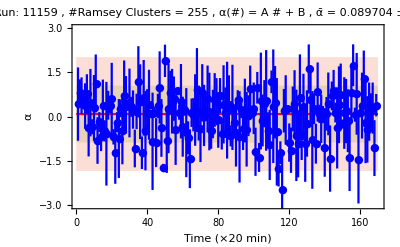

```mathematica
fitalnreal1m=Mean[fitsa[[;;,1]][[;;,1]]]
fitalnreal1s=StandardDeviation[fitsa[[;;,1]][[;;,1]]]
fitalnreal2m=Mean[fitsa[[;;,2]][[;;,1]]]
fitalnreal2s=StandardDeviation[fitsa[[;;,2]][[;;,1]]]
Show[{
EDAListPlot[dispplot,PlotStyle->{Blue},PlotMarkers->{Automatic,Medium},PlotRange->{{3.8422,3.8427},{-3,3}},Frame->True,FrameLabel->{"R","A=(N_↑)/(N_↑)"},TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},PlotLabel->"Run: 11159 , #Cycles = 1047 , A(R) = 2αCos[(R - SubscriptBox[R, 0])/(2  π)] , ᾱ = 0.018987 ± 0.965532",ImageSize->{1400}],
Plot[{-fitalnreal1m Cos[((xx-fitalnreal2m)*2Pi)/(180*mult)],
-fitalnreal1m Cos[((xx-fitalnreal2m)*2Pi)/(180*mult)]+rmserra,
-fitalnreal1m Cos[((xx-fitalnreal2m)*2Pi)/(180*mult)]-rmserra,
-fitalnreal1m Cos[((xx-fitalnreal2m)*2Pi)/(180*mult)]+2rmserra,
-fitalnreal1m Cos[((xx-fitalnreal2m)*2Pi)/(180*mult)]-2rmserra},{xx,3.8422,3.8427},PlotRange->{{3.8422,3.8427},{-3,3}},Frame->True,Filling->{{2->{3}},{4->{5}}},PlotStyle->{Red,None,None,None,None},PlotRange->Full,FrameLabel->{"R","A=(N_↑)/(N_↑)"},TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},PlotLabel->"Run: 11159, #Cycles = 1047 , A(R) = 2αCos[(R - SubscriptBox[R, 0])/(2  π)]  , ᾱ = 0.018987 ± 0.965532",ImageSize->{1400}]
}]
inset=Show[{
Histogram[errptsptres, Frame->True,FrameLabel->{"Ramsey-α Residual","#"},Axes->False,PlotRange->{{-0.25,0.25},{0,50}},TicksStyle->Directive[FontSize->40],LabelStyle->{14,Black,Bold},ImageSize->{250}],Plot[4.5PDF[NormalDistribution[0,Sqrt[2]RootMeanSquare[aerr]],x],{x,-0.25,0.25},Axes->False,PlotRange->{{0.5,0.9},{0,50}}, Frame->True,Filling->Axis,FrameLabel->{"Ramsey-α Residual","#"},TicksStyle->Directive[FontSize->40],LabelStyle->{14,Black,Bold},ImageSize->{300}],
EDAListPlot[Table[{HistogramList[errptsptres][[1]][[k]]-(HistogramList[errptsptres][[1]][[1]]-HistogramList[errptsptres][[1]][[2]])/2,{HistogramList[errptsptres][[2]][[k]],Sqrt[HistogramList[errptsptres][[2]][[k]]]}},{k,1,Dimensions[HistogramList[errptsptres][[2]]][[1]]}],PlotRange->{{0.5,0.9},{0,50}}, Frame->True,FrameLabel->{"Ramsey-α Residual","#"},TicksStyle->Directive[FontSize->40],LabelStyle->{14,Black,Bold},ImageSize->{300}]
}];
Show[{
Plot[{0 xx + fitaln[[2]][[1]], fitaln[[2]][[1]]+RootMeanSquare[fitsareal[[;;,1]][[;;,2]]],fitaln[[2]][[1]]-RootMeanSquare[fitsareal[[;;,1]][[;;,2]]],fitaln[[2]][[1]]+2RootMeanSquare[fitsareal[[;;,1]][[;;,2]]],fitaln[[2]][[1]]-2RootMeanSquare[fitsareal[[;;,1]][[;;,2]]]},{xx,0,dimfitsar+1},(*Epilog->Inset[inset,{60,.45}],*)Filling->{{3->{2}},{4->{5}}},Axes->False,PlotRange->{{1,dimfitsar+1},{-3,3}},Frame->True,FrameLabel->{"Time (×20 min)","α"},TicksStyle->Directive[FontSize->40],PlotStyle->{Red,None,None,None,None},LabelStyle->{28,Black},PlotLabel->"Run: 11159 , #Ramsey Clusters = 255 , α(#) = A # + B , ᾱ = 0.089704 ± 0.110832",ImageSize->{1400}],EDAListPlot[errptspt,PlotRange->{{1,dimfitsar+1},{-3,3}},PlotMarkers->{Automatic,Medium},Frame->True,FrameLabel->{"Time (×20 min)","α"},TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},PlotStyle->Blue,PlotLabel->"Run: 11395 , #Ramsey Clusters = 255 , α(#) = A # + B , ᾱ = 0.089704 ± 0.110832",ImageSize->{1400}]}]
```